```mathematica
i = 0;
f0[x_]:=Do[i++;
If[Mod[i,3]==0&&Mod[i,5]==0,Print["ThreeFive"],If[Mod[i,3]==0,Print["Three"],If[Mod[i,5]==0,Print["Five"],Print[i]]]],{i,20}];

f0[20]
```

2

Three

4

Five

Three

7

8

Three

Five

11

Three

13

14

ThreeFive

16

17

Three

19

Five

Three

```mathematica
ClearAll
```

ClearAll

```mathematica
var=x;
Do[var=1/(1+var),5];
Print[var]
```

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

```mathematica
newton[f_, df_,x0_,  eps_]:=(
Clear[i, lst, next];
i = 1;
lst = {x0};
Do[next = lst[[i]] - f[lst[[i]]]/df[lst[[i]]];
AppendTo[lst, next]; i++;
If[Abs[lst[[i]] - lst[[i-1]]]<eps, Break[]], Infinity];
Print[lst];
Return [lst])
```

```mathematica
eps = 10^(-5);

x0 = π - 0.1;
F1[x_] := Cos[x];
Df1[x_] = D[F1[x], x]
```

-Sin[x]

```mathematica
lst1  = newton[F1, Df1, x0, eps]
```

{3.04159,-6.92505,-8.26294,-7.82955,-7.85399,-7.85398}

{3.04159,-6.92505,-8.26294,-7.82955,-7.85399,-7.85398}

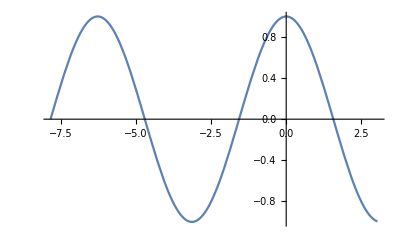

```mathematica
Plot[F1[x], {x, lst1[[1]], lst1[[-1]]}]
```

```mathematica
i=1;
```

```mathematica
plt = {}
```

{}

```mathematica
{}
```

```mathematica
Length[lst1]
```

6

```mathematica
Do[AppendTo[plt, Plot[F1[lst1[[i]]]+Df1[lst1[[i]]]*(x - lst1[[i]]), {x, -10, 10}, PlotStyle->Red]]; i++; If[i==7, Break[]], Infinity]
```

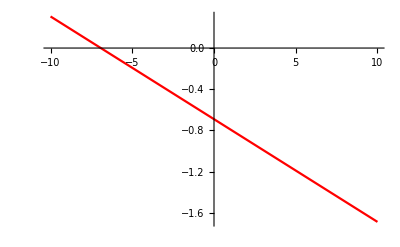
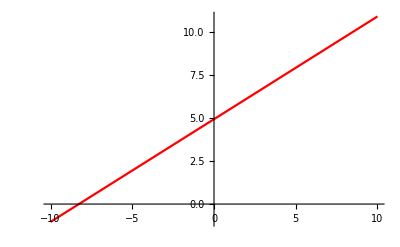
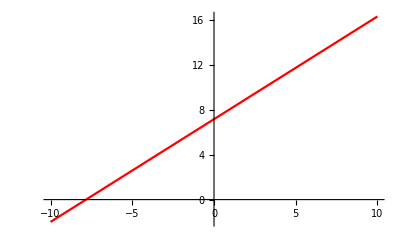
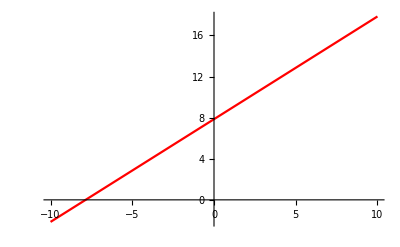
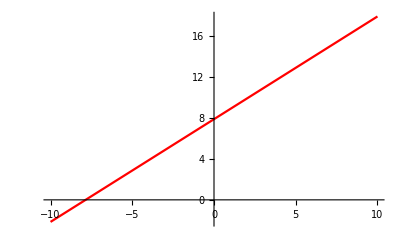
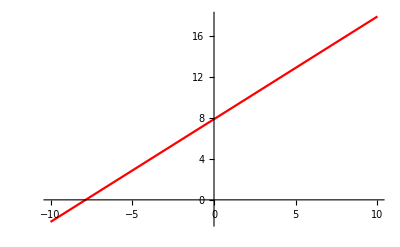

```mathematica
plt
```

```mathematica
Manipulate[Show[plt[[i]], Plot[F1[x], {x, lst1[[1]], lst1[[-1]]}, PlotStyle->Yellow], ListPlot[{{lst1[[i]], F1[lst[[i]]]}}]], {i, 1, Length[lst1] , 1}]
```

Part::partw: Part 6 of {18,18+Cot[18],18+Cot[18]+Cot[18+Cot[18]],18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]],18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]]+Cot[18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[Plus[«2»]]]]} does not exist.

Part::partw: Part 6 of {18.,17.12073512422131,17.28008824949198,17.27875959396203,17.27875959474386} does not exist.

Part::partw: Part 6 of {18.,17.1207,17.2801,17.2788,17.2788} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*решаем уравнение для 10 разных начальных значений х*)
```

```mathematica
a0 = 10 - π;
lstA0 = newton[F1, Df1, a0, eps]
```

{10-π,10-π+Cot[10],10-π+Cot[10]+Cot[10+Cot[10]],10-π+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]],10-π+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]],10-π+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]]]}

{10-π,10-π+Cot[10],10-π+Cot[10]+Cot[10+Cot[10]],10-π+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]],10-π+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]],10-π+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]+Cot[10+Cot[10]+Cot[10+Cot[10]]+Cot[10+Cot[10]+Cot[10+Cot[10]]]]]}

```mathematica
Length[lstA0]
```

6

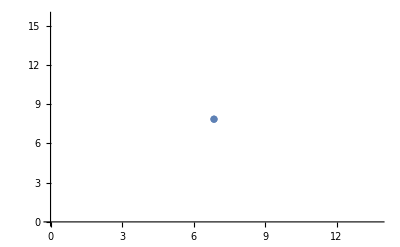

```mathematica
ListPlot[{{a0, lstA0[[6]]}}]
```

```mathematica
a1 = 15π - 0.3
```

46.8239

```mathematica
lstA1 = newton[F1, Df1, a1, eps]
```

{46.8239,43.5912,41.1662,44.1289,50.9013,52.2562,51.8097,51.8363,51.8363}

{46.8239,43.5912,41.1662,44.1289,50.9013,52.2562,51.8097,51.8363,51.8363}

```mathematica
Length[lstA1]
```

9

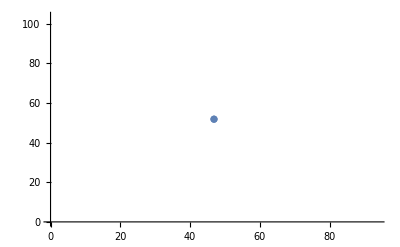

```mathematica
ListPlot[{{a1, lstA1[[9]]}}]
```

```mathematica
a2 = 1;
lstA2 = newton[F1, Df1, a2, eps]
```

{1,1+Cot[1],1+Cot[1]+Cot[1+Cot[1]],1+Cot[1]+Cot[1+Cot[1]]+Cot[1+Cot[1]+Cot[1+Cot[1]]],1+Cot[1]+Cot[1+Cot[1]]+Cot[1+Cot[1]+Cot[1+Cot[1]]]+Cot[1+Cot[1]+Cot[1+Cot[1]]+Cot[1+Cot[1]+Cot[1+Cot[1]]]]}

{1,1+Cot[1],1+Cot[1]+Cot[1+Cot[1]],1+Cot[1]+Cot[1+Cot[1]]+Cot[1+Cot[1]+Cot[1+Cot[1]]],1+Cot[1]+Cot[1+Cot[1]]+Cot[1+Cot[1]+Cot[1+Cot[1]]]+Cot[1+Cot[1]+Cot[1+Cot[1]]+Cot[1+Cot[1]+Cot[1+Cot[1]]]]}

```mathematica
Length[lstA2]
```

5

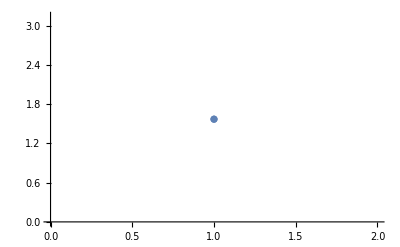

```mathematica
ListPlot[{{a2, lstA2[[5]]}}]
```

```mathematica
a3 = π/2+0.1
```

1.6708

```mathematica
lstA3 = newton[F1, Df1, a3, eps]
```

{1.6708,1.57046,1.5708,1.5708}

{1.6708,1.57046,1.5708,1.5708}

```mathematica
Length[lstA3]
```

4

```mathematica
4
```

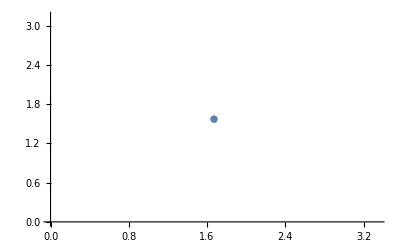

```mathematica
ListPlot[{{a3, lstA3[[4]]}}]
```

```mathematica
a4 = 8.34
```

8.34

```mathematica
lstA4 = newton[F1, Df1, a4, eps]
```

{8.34,7.81172,7.85401,7.85398,7.85398}

{8.34,7.81172,7.85401,7.85398,7.85398}

```mathematica
Length[lstA4]
```

5

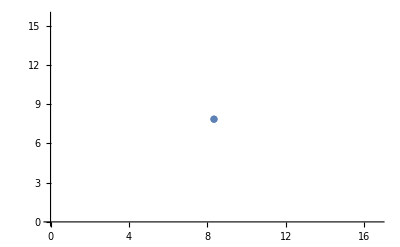

```mathematica
ListPlot[{{a4, lstA4[[5]]}}]
```

```mathematica
a5 = 0+0.0001
```

0.0001

```mathematica
lstA5 = newton[F1,Df1,a5,eps]
```

{0.0001,10000.,10003.1,10006.5,10008.1,10007.5,10007.5,10007.5,10007.5}

{0.0001,10000.,10003.1,10006.5,10008.1,10007.5,10007.5,10007.5,10007.5}

```mathematica
Length[lstA5]
```

9

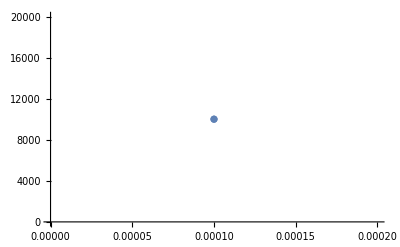

```mathematica
ListPlot[{{a5, lstA5[[9]]}}]
```

```mathematica
a6 = 122π/123
```

(122 π)/123

```mathematica
lstA6 = newton[F1, Df1, a6, eps]
```

{(122 π)/123,(122 π)/123-Cot[π/123],(122 π)/123-Cot[π/123]-Cot[π/123+Cot[π/123]],(122 π)/123-Cot[π/123]-Cot[π/123+Cot[π/123]]-Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]],(122 π)/123-Cot[π/123]-Cot[π/123+Cot[π/123]]-Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]]-Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]+Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]]]}

{(122 π)/123,(122 π)/123-Cot[π/123],(122 π)/123-Cot[π/123]-Cot[π/123+Cot[π/123]],(122 π)/123-Cot[π/123]-Cot[π/123+Cot[π/123]]-Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]],(122 π)/123-Cot[π/123]-Cot[π/123+Cot[π/123]]-Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]]-Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]+Cot[π/123+Cot[π/123]+Cot[π/123+Cot[π/123]]]]}

```mathematica
Length[lstA6]
```

5

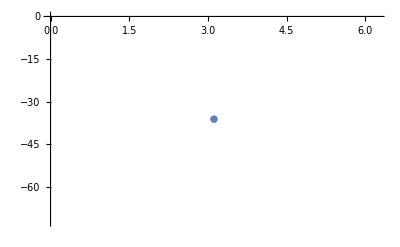

```mathematica
ListPlot[{{a6, lstA6[[5]]}}]
```

```mathematica
a7 = 30
```

30

```mathematica
lstA7 = newton[F1,Df1,a7,eps]
```

{30,30+Cot[30],30+Cot[30]+Cot[30+Cot[30]],30+Cot[30]+Cot[30+Cot[30]]+Cot[30+Cot[30]+Cot[30+Cot[30]]]}

{30,30+Cot[30],30+Cot[30]+Cot[30+Cot[30]],30+Cot[30]+Cot[30+Cot[30]]+Cot[30+Cot[30]+Cot[30+Cot[30]]]}

```mathematica
Length[lstA7]
```

4

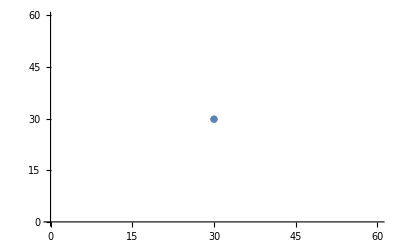

```mathematica
ListPlot[{{a7, lstA7[[4]]}}]
```

```mathematica
a8 = 2π/3
```

(2 π)/3

```mathematica
lstA8 = newton[F1,Df1,a8,eps]
```

{(2 π)/3,-1/(√3)+(2 π)/3,-1/(√3)+(2 π)/3+Tan[1/(√3)-π/6],-1/(√3)+(2 π)/3+Tan[1/(√3)-π/6]+Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]],-1/(√3)+(2 π)/3+Tan[1/(√3)-π/6]+Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]]+Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]-Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]]]}

{(2 π)/3,-1/(√3)+(2 π)/3,-1/(√3)+(2 π)/3+Tan[1/(√3)-π/6],-1/(√3)+(2 π)/3+Tan[1/(√3)-π/6]+Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]],-1/(√3)+(2 π)/3+Tan[1/(√3)-π/6]+Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]]+Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]-Tan[1/(√3)-π/6-Tan[1/(√3)-π/6]]]}

```mathematica
Length[lstA8]
```

5

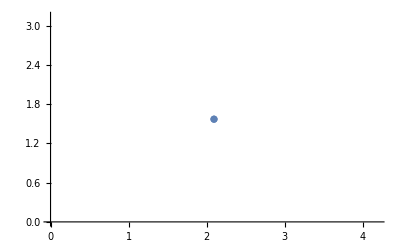

```mathematica
ListPlot[{{a8, lstA8[[5]]}}]
```

```mathematica
a9 = 15
```

15

```mathematica
lstA9= newton[F1,Df1,a9,eps]
```

{15,15+Cot[15],15+Cot[15]+Cot[15+Cot[15]],15+Cot[15]+Cot[15+Cot[15]]+Cot[15+Cot[15]+Cot[15+Cot[15]]],15+Cot[15]+Cot[15+Cot[15]]+Cot[15+Cot[15]+Cot[15+Cot[15]]]+Cot[15+Cot[15]+Cot[15+Cot[15]]+Cot[15+Cot[15]+Cot[15+Cot[15]]]]}

{15,15+Cot[15],15+Cot[15]+Cot[15+Cot[15]],15+Cot[15]+Cot[15+Cot[15]]+Cot[15+Cot[15]+Cot[15+Cot[15]]],15+Cot[15]+Cot[15+Cot[15]]+Cot[15+Cot[15]+Cot[15+Cot[15]]]+Cot[15+Cot[15]+Cot[15+Cot[15]]+Cot[15+Cot[15]+Cot[15+Cot[15]]]]}

```mathematica
Length[lstA9]
```

5

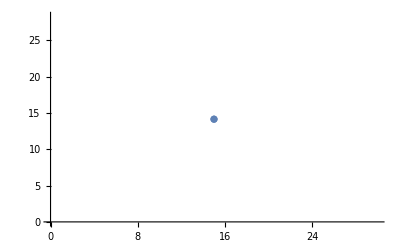

```mathematica
ListPlot[{{a9, lstA9[[5]]}}]
```

```mathematica
a10 = 18
```

18

```mathematica
lstA10 = newton[F1,Df1,a10,eps]
```

{18,18+Cot[18],18+Cot[18]+Cot[18+Cot[18]],18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]],18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]]+Cot[18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]]]}

{18,18+Cot[18],18+Cot[18]+Cot[18+Cot[18]],18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]],18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]]+Cot[18+Cot[18]+Cot[18+Cot[18]]+Cot[18+Cot[18]+Cot[18+Cot[18]]]]}

```mathematica
Length[lstA10]
```

5

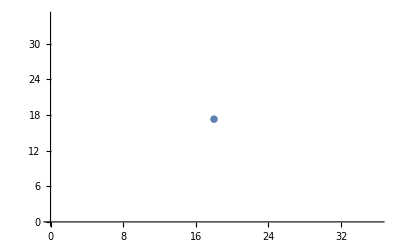

```mathematica
ListPlot[{{a10,  lstA10[[5]]}}]
```

```mathematica
(*можно заметить, что метод в зависимости от различных значений начальной точки сходится к разным результатам за разное число итераций*)
(*ЧАСТЬ 3*)
```

```mathematica
ClearAll[F1, x0, lst, lst1, plt]
```

```mathematica
newtonRestricted[f_, df_,x0_,  eps_]:=(
Clear[i, lst, next];
i = 1;
lst = {x0};
Do[
next = lst[[i]] - f[lst[[i]]]/df[lst[[i]]];
AppendTo[lst, next];
 i++;
If[i==10, Break[]];
If[Abs[lst[[i]] - lst[[i-1]]]<eps, Break[]],
 Infinity];
Print[lst];
Return [lst])
```

```mathematica
F[x_]:= x^3 - 2x + 2;
Df[x_] = D[F[x], x]
X0 = 0;
```

-2+3 x^2

```mathematica
lst1 = newtonRestricted[F, Df, X0, eps]
```

{0,1,0,1,0,1,0,1,0,1}

{0,1,0,1,0,1,0,1,0,1}

```mathematica
plt = {}
```

{}

```mathematica
Length[lst]
```

10

```mathematica
i = 1
```

1

```mathematica
Do[AppendTo[plt, Plot[F[lst1[[i]]]+Df[lst1[[i]]]*(x - lst1[[i]]), {x, -10, 10}, PlotStyle->Red]]; i++; If[i==11, Break[]], Infinity]
```

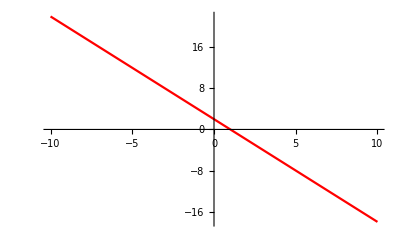
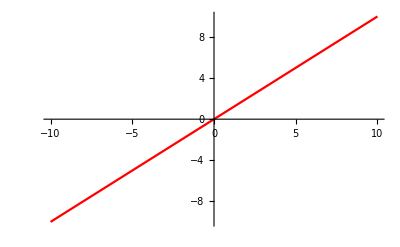
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plt
```

```mathematica
Manipulate[Show[plt[[i]], Plot[F[x], {x, -10,10}, PlotStyle->Yellow], ListPlot[{{lst1[[i]], F[lst1[[i]]]}}]], {i, 1, Length[lst1] , 1}]
```

```mathematica
(*что не так? можно заметить, что метод не сходится, потому что входит в бесконечный цикл. вероятно для нахождения производной точки 0 и 1 не очень хороши, попробуем другие точки...*)
```

```mathematica
x1 = -1;
lst11 = newtonRestricted[F, Df, x1, eps]
```

{-1,-4,-65/23,-573584/267191,-207783376707689575/112783158600027673,-20810863374452025770902657749303923594566723970109184/11738664365004664164025122835669512960860097115666441,-(10630562980985691415823849209646518825549374060163484215562870287250170737220713178309381124460793008383447183808908444992632030847680355949122166419540945625/6008339221564156383493619070748009814182117710159470253406864806054508604582633915801991012277731400965655713123367453366027639847293702887808916397556323623),-(2836499581404033632145027017613188331331316916753065822354998966002272449887438210339101346573436659581867591295858348667458839081131955263838111751329061219107037039030383684907462908102849189621503593179372252340096593794245165674495436182551117698182896189185996032237708524341944239438202399364918886248290997542636356107075686495847457926073858369427555179452731873126733008186914996067396747182070550980971006037688892980225089344158108457008090875455772416905641984/1603183088715993933287972475619778581776788094026539757871913443298826436210270775165354914093792746576646980784204221846314707050965935793043156184479073423230789651978098419994153441879822504067248062511770966902157166118924967533895972844472774974713982446631639102572068674703863792470418214376349106232372111097889411443130099689501018451585911717050833807642042876060317023257094278886986749213629178197925088720002998910827748641618389047124038626717827936653342391)}

{-1,-4,-65/23,-573584/267191,-207783376707689575/112783158600027673,-(20810863374452025770902657749303923594566723970109184/11738664365004664164025122835669512960860097115666441),-(10630562980985691415823849209646518825549374060163484215562870287250170737220713178309381124460793008383447183808908444992632030847680355949122166419540945625/6008339221564156383493619070748009814182117710159470253406864806054508604582633915801991012277731400965655713123367453366027639847293702887808916397556323623),-(2836499581404033632145027017613188331331316916753065822354998966002272449887438210339101346573436659581867591295858348667458839081131955263838111751329061219107037039030383684907462908102849189621503593179372252340096593794245165674495436182551117698182896189185996032237708524341944239438202399364918886248290997542636356107075686495847457926073858369427555179452731873126733008186914996067396747182070550980971006037688892980225089344158108457008090875455772416905641984/1603183088715993933287972475619778581776788094026539757871913443298826436210270775165354914093792746576646980784204221846314707050965935793043156184479073423230789651978098419994153441879822504067248062511770966902157166118924967533895972844472774974713982446631639102572068674703863792470418214376349106232372111097889411443130099689501018451585911717050833807642042876060317023257094278886986749213629178197925088720002998910827748641618389047124038626717827936653342391)}

```mathematica
Length[lst11]
```

8

```mathematica
plt11 = {}
```

{}

```mathematica
i = 1
```

1

```mathematica
Do[AppendTo[plt11, Plot[F[lst11[[i]]]+Df[lst11[[i]]]*(x - lst11[[i]]), {x, -10, 10}, PlotStyle->Red]]; i++; If[i==9, Break[]], Infinity]
```

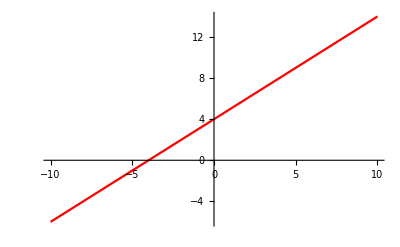
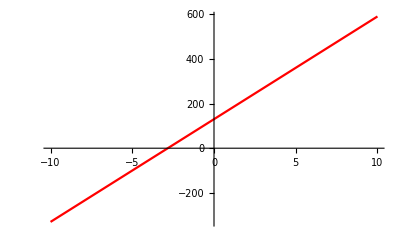
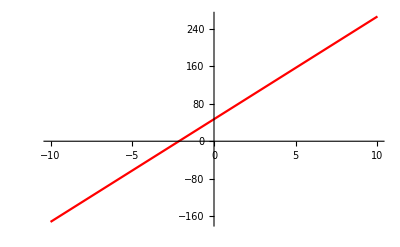
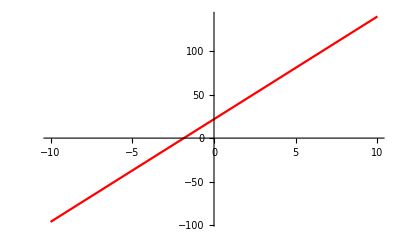
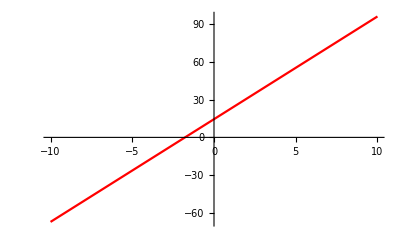
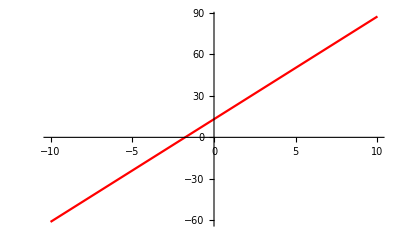
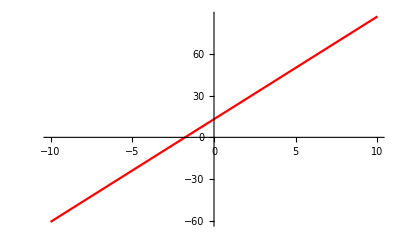
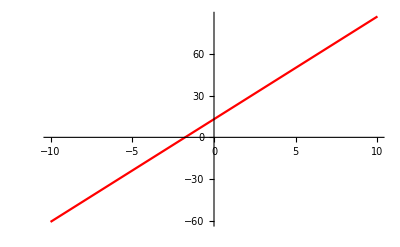

```mathematica
plt11
```

```mathematica
Manipulate[Show[plt11[[i]], Plot[F[x], {x, -10,10}, PlotStyle->Yellow], ListPlot[{{lst11[[i]], F[lst11[[i]]]}}]], {i, 1, Length[lst11] , 1}]
```

```mathematica
(*такое ощущение, что на этот раз метод сошелся*)
```

```mathematica
X2 = 0.5
```

0.5

```mathematica
lst2 = newtonRestricted[F, Df, X2, eps]
```

{0.5,1.4,0.898969,-1.28878,-2.10577,-1.8292,-1.77172,-1.7693,-1.76929}

{0.5,1.4,0.898969,-1.28878,-2.10577,-1.8292,-1.77172,-1.7693,-1.76929}

```mathematica
Length[lst2]
```

9

```mathematica
plt2 = {}
```

{}

```mathematica
i = 1
```

1

```mathematica
Do[AppendTo[plt2, Plot[F[lst2[[i]]]+Df[lst2[[i]]]*(x - lst2[[i]]), {x, -10, 10}, PlotStyle->Red]]; i++; If[i==10, Break[]], Infinity]
```

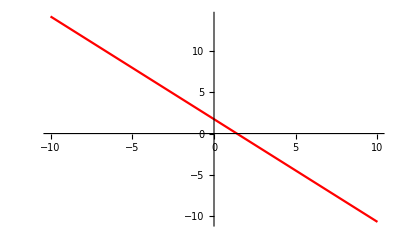
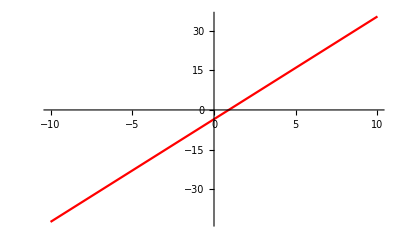
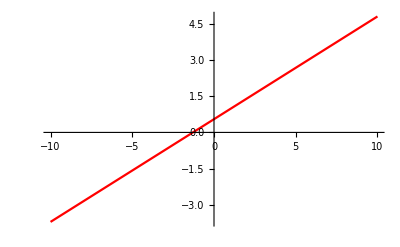
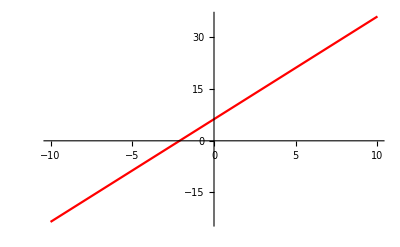
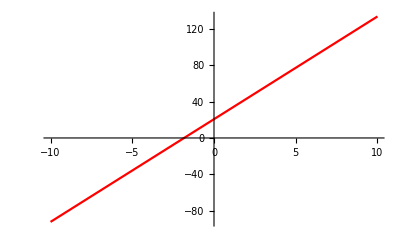
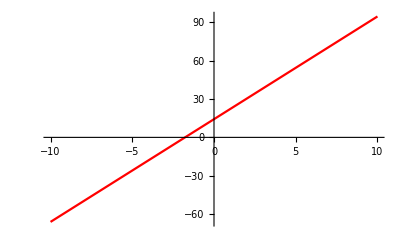
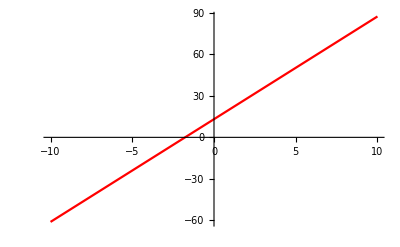
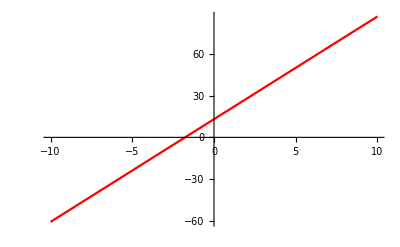

```mathematica
plt2
```

```mathematica
Manipulate[Show[plt2[[i]], Plot[F[x], {x, -10,10}, PlotStyle->Yellow], ListPlot[{{lst2[[i]], F[lst2[[i]]]}}]], {i, 1, Length[lst2] , 1}]
```

```mathematica
(*при х0 = 0.5 метод тоже сходится*)
```